# Jacobi’s Method

In this notebook we will take a look at Jacobi’s Method for solving linear systems.

```mathematica
A={{10,-1,2,0},{-1,11,-1,3},{2,-1,10,-1},{0,3,-1,8}};
A//MatrixForm
```

(10 | -1 | 2 | 0
-1 | 11 | -1 | 3
2 | -1 | 10 | -1
0 | 3 | -1 | 8)

We need to divide the Matrix A into the three pieces. It would be nice to have Mathematica do this for us... that sounds like a good homework problem!

```mathematica
Di=DiagonalMatrix[{10,11,10,8}];
Di//MatrixForm
```

(10 | 0 | 0 | 0
0 | 11 | 0 | 0
0 | 0 | 10 | 0
0 | 0 | 0 | 8)

```mathematica
U=-{{0,-1,2,0},{0,0,-1,3},{0,0,0,-1},{0,0,0,0}};
U//MatrixForm
```

(0 | 1 | -2 | 0
0 | 0 | 1 | -3
0 | 0 | 0 | 1
0 | 0 | 0 | 0)

```mathematica
L=-{{0,0,0,0},{-1,0,0,0},{2,-1,0,0},{0,3,-1,0}};
L//MatrixForm
```

(0 | 0 | 0 | 0
1 | 0 | 0 | 0
-2 | 1 | 0 | 0
0 | -3 | 1 | 0)

Let’s just make sure we did it right!

```mathematica
Di-L-U-A//MatrixForm
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

Now we define b for this example.

```mathematica
b={6,25,-11,15};
MatrixForm[b]
```

(6
25
-11
15)

```mathematica
T=Inverse[Di].(L+U);
T//MatrixForm
```

(0 | 1/10 | -1/5 | 0
1/11 | 0 | 1/11 | -3/11
-1/5 | 1/10 | 0 | 1/10
0 | -3/8 | 1/8 | 0)

```mathematica
c=Inverse[Di].b;
c//MatrixForm
```

(3/5
25/11
-11/10
15/8)

Mathematica is, of course, happy to tell us the solution via the LinearSolve function. Let’s take a look so we can compare it to the iterations of Jacobi’s Method.

```mathematica
sol=LinearSolve[A,b]
```

{1,2,-1,1}

We will use Nest to perform the iteration, so let’s define each step as a function of the vector x. Note that the matrix product is . in Mathematica. The operator * will take the entry-wise product.

```mathematica
It[{x_,T_,c_}]:={T.x+c,T,c}
```

```mathematica
N[It[{{0,0,0,0},T,c}]][[1]]
```

{0.6,2.27273,-1.1,1.875}

Now we can let the iteration run!

```mathematica
N[Nest[It,{{0,0,0,0},T,c},10]][[1]]
```

{1.00012,1.99977,-0.999828,0.999786}

Now let’s take a look at the (l_infinity) error.

```mathematica
Error[x_,s_]:=Norm[x-s,Infinity]
```

```mathematica
Error[N[Nest[It,{{0,0,0,0},T,c},10][[1]]],sol]
```

0.000232053

```mathematica
errors=Table[Error[N[Nest[It,{{0,0,0,0},T,c},i][[1]]],sol],{i,1,10}]
```

{0.875,0.284091,0.130881,0.0463042,0.0213505,0.00775874,0.00359431,0.0013297,0.00061919,0.000232053}

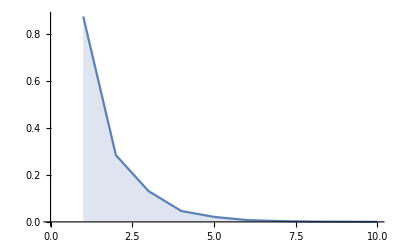

```mathematica
ListLinePlot[errors,Filling->Axis,PlotRange->Full]
```